```mathematica
data = {{0,0},{1,2},{2,4},{3,6},{4,7},{5,3},{6,2},{7,7},{8,6}};
```

```mathematica
ans =Fit[data,{1,x,x^2,x^3,x^4,Cos[x],x^5,Sin[x]},x];
```

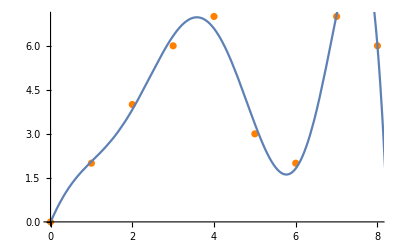

```mathematica
Show[ListPlot[data,PlotStyle->Orange],Plot[ans,{x,0,15}]]
```

```mathematica
data2= {5.,9.,8.,10.,6.1,10.4,9.1,11.6,7.5,12.1,10.4,13.5,9.,14.1,11.9,15.7,10.8,16.4,13.7,18.3,12.9,19.,15.8,21.2,
15.3,22.1,18.3,24.6};
```

```mathematica
ans2 =  Fit[data2,{1,x,x^2,x^3,x^4,Cos[x],x^5,Sin[x]},x];
```

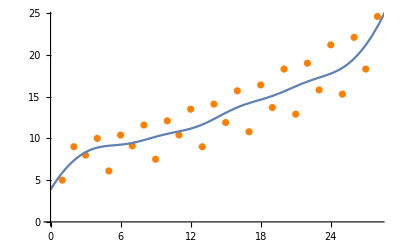

```mathematica
Show[ListPlot[data2,PlotStyle->Orange],Plot[ans2,{x,0,30}]]
```

```mathematica
ans3 = TimeSeriesModelFit[data2];
```

```mathematica
Normal[ans3];
```

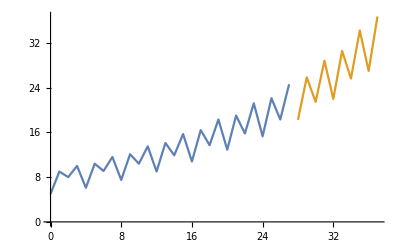

tsm

```mathematica
ListLinePlot[{ans3["TemporalData"],TimeSeriesForecast[ans3,{10}]}]
```